# Galáxia NGC 7339

## Tabelas

```mathematica
data = Import["C:\\Users\\Leoleo\\Desktop\\TCC\\Mathematica\\data_new\\7339.dat"];
RC=Table[{data[[i,1]],data[[i,3]]},{i,1,15}];
Rgas=Table[{data[[i,1]],data[[i,4]]},{i,1,15}];
Erro = Table[data[[i,5]],{i,1,15}];
radii=Part[Transpose[data],1];
Vel=Part[Transpose[data],3];
err=Part[Transpose[data],5];
TableForm[data,TableHeadings->{{"NGC 1090"},{"Raio","","Vtotal","Vgas","Erro"}}]
```

| Raio |  | Vtotal | Vgas | Erro
NGC 1090 | 0.17069 | 3.53707 | 25.81 | -1.34586 | 5.54
 | 0.512069 | 4.03218 | 63.14 | -3.60897 | 4.02
 | 0.853448 | 4.80899 | 88.79 | -5.43247 | 3.98
 | 1.19483 | 5.86751 | 118.89 | -6.37706 | 9.48
 | 1.53621 | 6.75684 | 116.06 | -5.77815 | 2.26
 | 1.87759 | 7.50929 | 127.75 | -1.61714 | 2.62
 | 2.21897 | 7.72679 | 135.88 | 6.71423 | 2.8
 | 2.56034 | 7.79803 | 140. | 8.8814 | 3.16
 | 2.90172 | 8.19568 | 144.13 | 11.4071 | 2.33
 | 3.2431 | 8.44312 | 153.73 | 15.0866 | 2.92
 | 3.58448 | 8.38166 | 150.78 | 18.7424 | 3.08
 | 3.92586 | 7.73976 | 160.02 | 22.3997 | 3.01
 | 4.26724 | 6.62754 | 161.4 | 24.5162 | 2.14
 | 4.66724 | 5.80733 | 169.09 | 26.0432 | 10.14
 | 5.43103 | 4.14981 | 159.5 | 29.4017 | 2.04

## Interpolação

```mathematica
Igas = Interpolation[Rgas]
```

InterpolatingFunction[{{0.17069, 5.43103}}, <>]

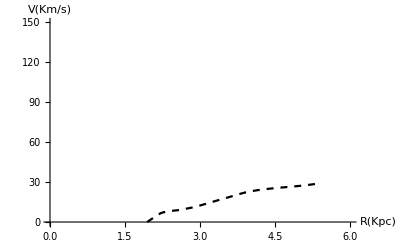

```mathematica
Gas =Plot[Igas[x],{x,0.27931,5.4},PlotStyle->{Black,Dashed},AxesLabel->{"R(Kpc)","V(Km/s)"},PlotRange->{{0,6},{0,150}}]
```

## Definindo Equações

```mathematica
Vd[r_,M_]:=1/(2 Rd)(G (M *10^9) (r/Rd)^2) (BesselI[0,r/(2 Rd)] BesselK[0,r/(2 Rd)]-BesselI[1,r/(2 Rd)] BesselK[1,r/(2 Rd)]);
Vme[r_,R_,P_]:=(6.4 G ((P *10^7) R^3) (1/2 Log[(r/R)^2+1]+Log[r/R+1]-ArcTan[r/R]))/r;
G:=4.302/10^6;
Rd:=1.5;
Vt[r_,M_,R_,P_]:=Sqrt[Vd[r,M]+Vme[r,R,P]+Igas[r]^2]
```

## Ajuste

```mathematica
Ajuste= NonlinearModelFit[RC,Vt[r,M,R,P],{{P,1,5},{M,1,50},{R,1,10}},r,Weights->Erro^-2]
```

FittedModel[√(9085.89 r^2 (BesselI[0,0.333333 r] BesselK[0,0.333333 r]-BesselI[1,0.333333 r] BesselK[1,0.333333 r])+(«18» («1»))/r+(InterpolatingFunction[{{0.17069, 5.43103}}, <>][r])^2)]

```mathematica
Ajuste["BestFitParameters"]
```

{P→6.39299,M→14.2561,R→4.98007}

```mathematica
Ajuste["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
P | 6.39299 | 3.43751 | 1.85977 | 0.0875965
M | 14.2561 | 1.40708 | 10.1317 | 3.10867×10^-7
R | 4.98007 | 2.06756 | 2.40867 | 0.0329929

```mathematica
a=Plot[Ajuste[x],{x,0,5.4},AxesOrigin->{0,0}];
Show[a,ListPlot[RC]];
```

InterpolatingFunction::dmval: Input value {0.000110314} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

## Gráficos

```mathematica
Needs["ErrorBarPlots`"]
```

```mathematica
RCtotal = Plot[Ajuste[r],{r,0,5.4}, PlotStyle->Black,PlotRange->{{0,6},{0,160}}];
Vstars = Plot[Sqrt[Vd[r,M]]/.M->14.256 ,{r,0,6},PlotStyle->{Black,Dotted}];
Vhalo = Plot[Sqrt[Vme[r,R,P]]/.{R->6.39,P->4.98},{r,0,6},PlotStyle->{Black,DotDashed}];
VRC = ErrorListPlot[{Table[{RC[[i]],ErrorBar[Erro[[i]]]},{i,15}]},PlotStyle->Directive[PointSize[0.02],Black]];
Teste = Plot[Vt[r,M,R,P]/.{M->14.256,R->6.39,P->4.98},{r,0,5.4},PlotStyle->Black, PlotRange->{{0,5.5},{0,200}}];
```

InterpolatingFunction::dmval: Input value {0.000110314} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.000110314} lies outside the range of data in the interpolating function. Extrapolation will be used.

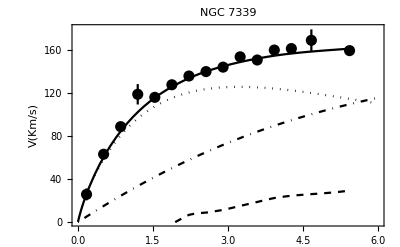

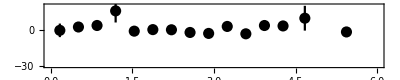

```mathematica
Graf1 =Show[Teste,VRC,Vstars,Vhalo,Gas,Frame->True,PlotRange->{{0,6},{0,180}},PlotLabel->Style["NGC 7339",Black],FrameStyle->Black, FrameLabel->{"","V(Km/s)"}]

Graf2 =ErrorListPlot[{Table[{Table[{data[[i,1]],Ajuste["FitResiduals"][[i]]},{i,15}][[i]],ErrorBar[Erro[[i]]]},{i,15}]},PlotStyle->Directive[PointSize[0.02],Black],PlotRange->{{0,6},{-30,20}},Frame->True,FrameStyle->Black,FrameLabel->{"R (Kpc)",""},AspectRatio->0.2]
```

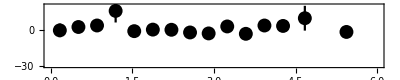

```mathematica
Graph1=Show[Teste,VRC,Vstars,Vhalo,Gas, Frame->True,PlotRange->{{0,26},{0,200}},FrameStyle->Black,PlotLabel->Style["ESO 287-G13",Black],FrameLabel->{"","V(Km/s)"}]
Graph2 =ErrorListPlot[{Table[{Table[{data[[i,1]],Ajuste["FitResiduals"][[i]]},{i,26}][[i]],ErrorBar[Erro[[i]]]},{i,26}]}, PlotStyle->Directive[PointSize[0.025],Black],  PlotRange->{{0,26},{-40,10}},Frame->True,FrameStyle->Black,FrameLabel->{"R (Kpc)",""}, AspectRatio->0.2]

chi2[M_,P_,R_]:=N[Plus@@Table[(Vel[[i]]-Vt[radii[[i]],M,P,R])^2/(err[[i]])^2,{i,Dimensions[radii][[1]]}]]
```

```mathematica
BestFit = Timing[NMinimize[{chi2[M,P,R],M>1&&M<30&&P>1 && P<10 && R>1 && R<10},{M,P,R}]]
```

{0.796875,{13.2264,{M→14.2561,P→4.98007,R→6.39299}}}

InterpolatingFunction::dmval: Input value {0.000110927} lies outside the range of data in the interpolating function. Extrapolation will be used.

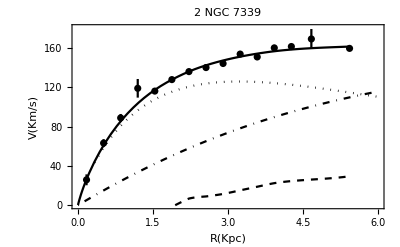

```mathematica
X2 =Plot[{Vt[r,M,P,R]/. {M->14.2561,P->4.98,R->6.393}},{r,0,5.43},PlotStyle->Black];
Graf2 =Show[X2,VRC,Vstars,Vhalo,Gas,Frame->True,PlotRange->{{0,6},{0,180}},PlotLabel->"2 NGC 7339", FrameLabel->{"R(Kpc)","V(Km/s)"}]
```

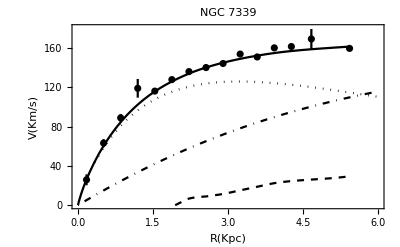

```mathematica
Show[Graf1]
```